# Leads connected to 1 - 10 and 1 to 10

# a1 and a2

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_,m_]:= t*IdentityMatrix[m]
```

```mathematica
Clear[T]
```

```mathematica
T[t_,m_]:=Module[{MAT=0*IdentityMatrix[30]},MAT[[m;;m,m;;m]]=t*IdentityMatrix[1];MAT]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardul/PhD_new/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,3,0.01]}]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+1]]]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentration]=Table[SortBy[Join[RandomSample[Join[s[2,29,2,15]],concentration],RandomSample[Join[s[2,29,16,29]],total-concentration]],First],10000]
```

```mathematica
dist[10,7][[100]]
```

{{7,13},{8,4},{12,8},{13,23},{16,5},{18,11},{23,12},{23,29},{26,20},{28,4}}

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,30]]
```

```mathematica
Clear[SLLEAD]
```

```mathematica
SLLEAD[ω_,pos1_]:=Module[{MAT=0*IdentityMatrix[30]},MAT[[pos1;;pos1,pos1;;pos1]]=LEFT[ω,1];MAT]
```

```mathematica
SRLEAD[ω_,pos2_]:=Module[{MAT=0*IdentityMatrix[30]},MAT[[pos2;;pos2,pos2;;pos2]]=LEFT[ω,1];MAT]
```

```mathematica
device1[ω_,pos1_]:=Inverse[IdentityMatrix[30]-g[ω,0.0001,1,0].T[1,pos1].SLLEAD[ω,pos1].T[1,pos1]].g[ω,0.0001,1,0]
```

```mathematica
TLD[t_,pos2_]:=Module[{mat=RandomInteger[0,{30,30}]},ReplacePart[mat,{{pos2,pos2}}->t]]
```

```mathematica
F[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_,unitcell_]:=Module[{J=β[ω,δ,t,ϵ,30],abc=dist[total,concentration][[number]]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_,pos1_,pos2_]:=
Module[{abc=dist[total,concentration][[number]]},
recurs=Module[{J1= device1[ω,pos1]},
Do[
J1=Inverse[IdentityMatrix[30]-Inverse[F[ω,δ,t,ϵ,ϵ1,total,concentration,number,unitcell]].T1[1,30].J1.T1[1,30]].Inverse[F[ω,δ,t,ϵ,ϵ1,total,concentration,number,unitcell]],{unitcell,30}];J1];ir=Inverse[IdentityMatrix[30]-SRLEAD[ω,pos2].TLD[1,pos2].recurs.TLD[1,pos2]].SRLEAD[ω,pos2];il=Inverse[IdentityMatrix[30]-recurs.TLD[1,pos2].SRLEAD[ω,pos2].TLD[1,pos2]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1,pos2].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1,pos2].grr1.TLD[1,pos2]-TLD[1,pos2].GNON1.TLD[1,pos2].GNON1]];TRA]
```

```mathematica
Clear[inp,ca]
```

```mathematica
inp[w_,n_]:=inp[w,n]=Table[Table[CA[w,0.0001,1,0,1,10,7,n,y,x],{x,1,30,2}],{y,2,30,2}]
```

```mathematica
ca[w_,z_]:=ca[w,z]=Mean[ParallelTable[Table[Table[CA[w,0.0001,1,0,1,10,z,num,y,x],{x,1,30,2}],{y,2,30,2}],{num,100}]]
```

```mathematica
Monitor[Table[Monitor[Table[Export["~/PhD_new/multielectrode_"<>ToString[w]<>"_"<>ToString[x]<>"_imp.dat",ca[w,x]],{x,10}],x],{w,Range[0.15,1.5,0.5]}],w]
```

{{~/PhD_new/multielectrode_0.15_1_imp.dat,~/PhD_new/multielectrode_0.15_2_imp.dat,~/PhD_new/multielectrode_0.15_3_imp.dat,~/PhD_new/multielectrode_0.15_4_imp.dat,~/PhD_new/multielectrode_0.15_5_imp.dat,~/PhD_new/multielectrode_0.15_6_imp.dat,~/PhD_new/multielectrode_0.15_7_imp.dat,~/PhD_new/multielectrode_0.15_8_imp.dat,~/PhD_new/multielectrode_0.15_9_imp.dat,~/PhD_new/multielectrode_0.15_10_imp.dat},{~/PhD_new/multielectrode_0.65_1_imp.dat,~/PhD_new/multielectrode_0.65_2_imp.dat,~/PhD_new/multielectrode_0.65_3_imp.dat,~/PhD_new/multielectrode_0.65_4_imp.dat,~/PhD_new/multielectrode_0.65_5_imp.dat,~/PhD_new/multielectrode_0.65_6_imp.dat,~/PhD_new/multielectrode_0.65_7_imp.dat,~/PhD_new/multielectrode_0.65_8_imp.dat,~/PhD_new/multielectrode_0.65_9_imp.dat,~/PhD_new/multielectrode_0.65_10_imp.dat},{~/PhD_new/multielectrode_1.15_1_imp.dat,~/PhD_new/multielectrode_1.15_2_imp.dat,~/PhD_new/multielectrode_1.15_3_imp.dat,~/PhD_new/multielectrode_1.15_4_imp.dat,~/PhD_new/multielectrode_1.15_5_imp.dat,~/PhD_new/multielectrode_1.15_6_imp.dat,~/PhD_new/multielectrode_1.15_7_imp.dat,~/PhD_new/multielectrode_1.15_8_imp.dat,~/PhD_new/multielectrode_1.15_9_imp.dat,~/PhD_new/multielectrode_1.15_10_imp.dat}}

```mathematica
average[0.15,1]
```

```mathematica
average[w_,x_]:=Import["~/PhD_new/multielectrode_"<>ToString[w]<>"_"<>ToString[x]<>"_imp.dat"]
```

```mathematica
misfit[w_,n_]:=Monitor[Table[Total[Total[Reverse[Abs[ca[w,x]-inp[w,n]]]]],{x,10}],x]
```

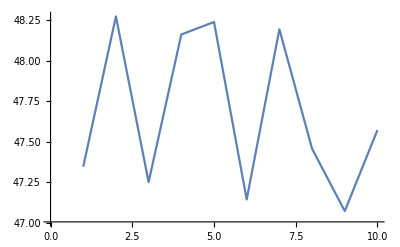

```mathematica
misfit[0.01,1]//ListLinePlot
```

```mathematica
Monitor[Table[Total[ParallelTable[misfit[w,n],{w,Range[0.15,1.5,1]}]],{n,1,10}],n]
```

{{397.714,384.05,379.88,393.798,391.907,381.666,383.656,392.209,400.451,380.012},{351.455,328.691,335.994,352.519,335.652,342.007,341.797,345.442,344.505,314.027},{372.935,359.741,364.859,377.144,372.792,368.392,373.495,376.793,372.217,362.417},{339.683,328.123,330.145,344.381,336.444,335.954,336.171,342.678,333.511,321.126},{391.666,377.698,381.522,395.595,385.294,380.754,384.145,399.092,392.695,367.155},{371.626,355.244,358.338,370.479,371.925,364.225,366.637,378.095,374.46,360.385},{470.296,478.914,475.823,468.837,467.331,473.725,471.252,470.976,467.775,474.137},{368.441,363.796,363.832,365.708,375.089,362.693,363.344,382.109,375.633,373.688},{436.228,438.185,428.244,433.778,446.291,427.364,426.298,444.674,444.945,447.904},{340.893,325.438,328.112,343.95,330.833,329.92,332.992,344.103,335.747,308.71}}

```mathematica
Manipulate[ListLinePlot[%60[[x]]],{x,Range[1,10,1]}]
```

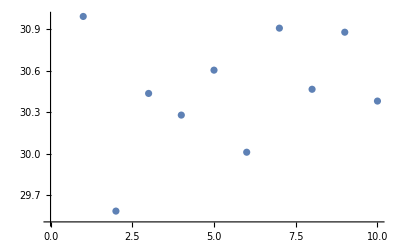

```mathematica
ListPlot[{30.99408498249,29.585539924183404,30.43702369713538,30.280283897479805,30.605531895961946,30.011541839012544,30.909504357928157,30.46716163794877,30.88015028311886,30.381801833988774}]
```

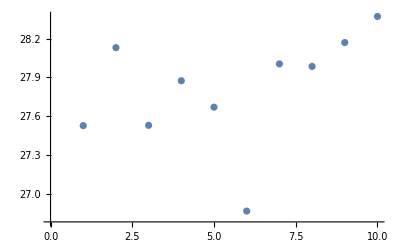

```mathematica
ListPlot[{27.52859466592616,28.129731390099586,27.53089298967678,27.87464576164836,27.670942849600998,26.86994526267719,28.00456889620717,27.985116371297988,28.16900931982538,28.370085712554207}]
```

```mathematica
Table[Table[Tr[misfit[y][[x]]],{x,10}],{y,Range[0.01,1.51,0.1]}]
```

$Aborted

```mathematica
Table[inp[w],{w,0.01,1.51,0.1}]
```

{1}
 |  |  |  |

```mathematica
Monitor[Table[Import["~/PhD_new/multiprobes_Energy_"<>ToString[w]<>"_10.dat"],{w,Range[0.1,1.51,0.05]}],w]
```

{1}
 |  |  |  |

```mathematica
Dimensions[%45]
```

{29,10,900}

```mathematica
%45[[1]][[1]]
```

```mathematica
Table[Abs[%48[[1]]-%45[[1]][[x]]],{x,}]
```

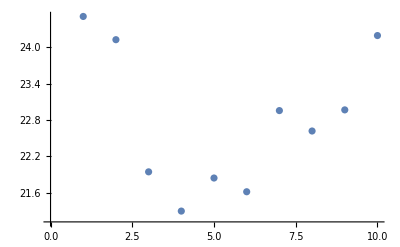

```mathematica
ListPlot[{24.50606392785399,24.12303492673244,21.94374329531463,21.29662455049337,21.841872473992233,21.615451720856043,22.953817494037164,22.617151528849114,22.965513634307822,24.191218819399296}]
```

```mathematica
Manipulate[MatrixPlot[%141[[y]],ColorFunction->"BlueGreenYellow"],{y,10}]
```

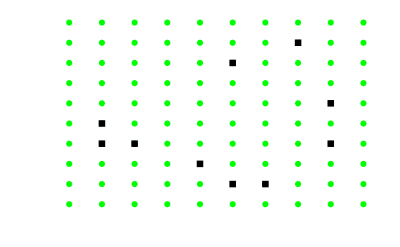

```mathematica
ListPlot[{Join[s[1,10,1,10]],dist[10,7][[1]]},PlotMarkers->Automatic,PlotStyle->{Green,Black},Axes->False]
```